## Analytical Mixing Model, v1 (50-50 mixes only) Last updated: February 5, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n

(*f3:=1/2*P1A[s1,μ1A,η](n/2-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](n/2-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η](n/2-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η](n/2-(n1B+n2B)) - τ*n2B*)
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ1A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ2A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ1B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ2B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
τ=0.2;
(*μ1A=10;μ2A=10;μ1B=20;μ2B=20;*)
α1A=k;α1B=k;α2A=k;α2B=k;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}≥0;
```

```mathematica
(*Off[Solve::ratnz];
(η=#;
(*eq=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];*)
(*eq2 = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];*)
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}];

Print[{"η = "<>ToString[#],Length@eq2,DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq2[[1]]]}];&)/@{1}(* {1,2,3,4,5,6,7}*)*)
```

```mathematica
Clear[δ1,δ2,α1A,α1B,α2A,α2B,n,μ1A,μ2A,μ1B,μ2B];
n=16.;(*μ1A=10.;μ2A=20.;μ1B=20.;μ2B=10.;*)
δ1=0.6; δ2=0.6;
(*Reduce[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0&&$Assumptions,{s1,s2,n1A,n2A,n1B,n2B}]*)
(*Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}]*)
μ1A =10 ; μ2A = 2*μ1A; μ1B = 2*μ1A; μ2B =μ1A;
α1A=2;α1B=α1A;α2A=α1A;α2B=α1A;

eq3=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}] ,$Assumptions];
eq4=DeleteDuplicates[FullSimplify[{n1A,n2A,n1B,n2B}/.eq3,$Assumptions]]
Length@eq4

f1
f2
f3
f4
f5
f6
```

{{8.21454,-3.41454,-3.41454,8.21454},{5.8376,0.0333253,-1.0376,4.76667},{4.71145,0.0885515,0.0885515,4.71145},{4.76667,-1.0376,0.0333253,5.8376}}

4

0.6-0.0625 (2 n1A+2 n1B)

0.6-0.0625 (2 n2A+2 n2B)

-0.2 n1A+((8.-n1A-n2A) s1^7)/(2 (10000000+s1^7))

-0.2 n2A+((8.-n1A-n2A) s2^7)/(2 (1280000000+s2^7))

-0.2 n1B+((8.-n1B-n2B) s1^7)/(2 (1280000000+s1^7))

-0.2 n2B+((8.-n1B-n2B) s2^7)/(2 (10000000+s2^7))

Why can’t the equilibria be computed when μ1B = μ2B = 2*μ1A???

```mathematica
FullSimplify[{f1,f2,f3,f4,f5,f6}/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B),n1B->(n δ1)/(α1A+α1B),n2B->(n δ2)/(α2A+α2B)} ] // MatrixForm
```

(0.
0.
(-4.8×10^6+1.12 s1^7)/(1.×10^7+s1^7)
(-6.144×10^8+1.12 s2^7)/(1.28×10^9+s2^7)
(-6.144×10^8+1.12 s1^7)/(1.28×10^9+s1^7)
(-4.8×10^6+1.12 s2^7)/(1.×10^7+s2^7))

```mathematica
eq2
```

## Analytical Mixing Model, v2 (mixes with different fractions of A individuals) Last updated: February 9, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n
f3:=1/2*P1A[s1,μ1A,η](f*n-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](f*n-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η]((1.-f)*n-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η]((1.-f)*n-(n1B+n2B)) - τ*n2B

f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ1A,η])*(f*n-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ2A,η])*(f*n-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ1B,η])*((1.-f)*n-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ2B,η])*((1.-f)*n-(n1B+n2B)) - τ*n2B
```

```mathematica
(*τ=1;*)
(*μ1A=10;μ2A=10;μ1B=10;μ2B=10;*)
μ1A=k;μ2A=k;μ1B=k;μ2B=k;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,f}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,f}≥0 && f≤1;
```

```mathematica
Off[Solve::ratnz];
(η=#;
eq=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];
(*eq2 = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];*)
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}];

Print[{"η = "<>ToString[#],Length@eq,FullSimplify@DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq],Length@eq2,FullSimplify@DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq2]}];&)/@ {1,2,3,4,5,6,7}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

{η = 1,1,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},2,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 2,4,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},8,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 3,9,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},18,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 4,16,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},32,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 5,25,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},50,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 6,36,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},72,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 7,49,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},98,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
η=3; δ1=0.6; δ2 = δ1 ; k = 10; τ=0.2; f = 0.5; n = 16;b =1;
α1A = 2; α2A = 2; α1B =b; α2B =b;
eqeq = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];
{s1,s2,n1A,n2A,n1B,n2B, (n1A+n2A+n1B+n2B)/n ,(n1A+n2A+n1B+n2B)/n≤ 1}/.eqeq// MatrixForm

DeleteDuplicates[f1/.eqeq]
DeleteDuplicates[f2/.eqeq]
```

(-14.7913 | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-14.7913 | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-14.7913 | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True)

{-1.11022×10^-16}

{-1.11022×10^-16}

OK, let’s plot these and see if we can get something similar to Chris’s results!

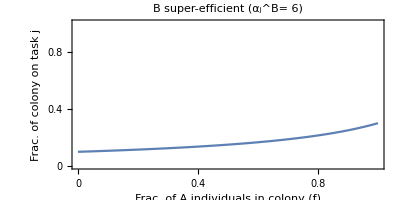

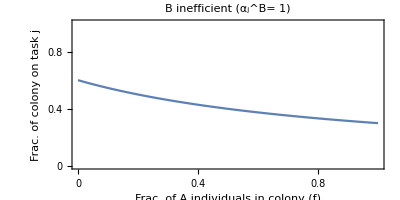

```mathematica
a1 = 2;
a2 = 6;
Plot[0.6/(f*a1+(1-f)*a2),{f,0,1},PlotRange->{{0,1},{0,1}},PlotLabel->"B super-efficient (α_j^B= 6)",
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Frac. of colony on task j",None},{"Frac. of A individuals in colony (f)",None}},FrameTicks->All, AspectRatio->1/2]

a2 = 1;
Plot[0.6/(f*a1+(1-f)*a2),{f,0,1},PlotRange->{{0,1},{0,1}},PlotLabel->"B inefficient (α_j^B= 1)",
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Frac. of colony on task j",None},{"Frac. of A individuals in colony (f)",None}},FrameTicks->All, AspectRatio->1/2]
```

## Changing the stimulus equations (50-50 mixes only) Last updated: February 13, 2019 What happens when the simulus equations are NOT normalized?? (See f1p and f2p below)

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
(*f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n*)
f1p:=n*δ1 -(α1A*n1A + α1B*n1B)
f2p:=n*δ2 -(α2A*n2A + α2B*n2B)

(*f3:=1/2*P1A[s1,μ1A,η](n/2-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](n/2-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η](n/2-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η](n/2-(n1B+n2B)) - τ*n2B*)
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ1A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ2A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ1B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ2B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
τ=0.2;
(*μ1A=10;μ2A=10;μ1B=10;μ2B=10;*)
μ1A=k;μ2A=k;μ1B=k;μ2B=k;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}≥0;
```

```mathematica
Off[Solve::ratnz];
(η=#;
eq=FullSimplify[Solve[f1p==0&&f2p==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];

Print[{"η = "<>ToString[#],Length@eq,DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq]}];&)/@ {1}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

{η = 1,2,{{(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B),(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B)}}}

$Aborted

```mathematica
Clear[δ1,δ2,α1A,α1B,α2A,α2B,n,μ1A,μ2A,μ1B,μ2B];
n=16.;(*μ1A=10.;μ2A=20.;μ1B=20.;μ2B=10.;*)
δ1=0.6; δ2=0.6;
(*Reduce[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0&&$Assumptions,{s1,s2,n1A,n2A,n1B,n2B}]*)
(*Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}]*)
μ1A =10 ; μ2A = 2*μ1A; μ1B = 2*μ1A; μ2B =μ1A;
α1A=2;α1B=α1A;α2A=α1A;α2B=α1A;

eq3=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}] ,$Assumptions];
eq4=DeleteDuplicates[FullSimplify[{n1A,n2A,n1B,n2B}/.eq3,$Assumptions]]
Length@eq4

f1
f2
f3
f4
f5
f6
```

{{8.21454,-3.41454,-3.41454,8.21454},{5.8376,0.0333253,-1.0376,4.76667},{4.71145,0.0885515,0.0885515,4.71145},{4.76667,-1.0376,0.0333253,5.8376}}

4

0.6-0.0625 (2 n1A+2 n1B)

0.6-0.0625 (2 n2A+2 n2B)

-0.2 n1A+((8.-n1A-n2A) s1^7)/(2 (10000000+s1^7))

-0.2 n2A+((8.-n1A-n2A) s2^7)/(2 (1280000000+s2^7))

-0.2 n1B+((8.-n1B-n2B) s1^7)/(2 (1280000000+s1^7))

-0.2 n2B+((8.-n1B-n2B) s2^7)/(2 (10000000+s2^7))

Why can’t the equilibria be computed when μ1B = μ2B = 2*μ1A???

```mathematica
FullSimplify[{f1,f2,f3,f4,f5,f6}/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B),n1B->(n δ1)/(α1A+α1B),n2B->(n δ2)/(α2A+α2B)} ] // MatrixForm
```

(0.
0.
(-4.8×10^6+1.12 s1^7)/(1.×10^7+s1^7)
(-6.144×10^8+1.12 s2^7)/(1.28×10^9+s2^7)
(-6.144×10^8+1.12 s1^7)/(1.28×10^9+s1^7)
(-4.8×10^6+1.12 s2^7)/(1.×10^7+s2^7))

```mathematica
eq2
```

## Different μ’s under symmetric task performance (50-50 mixes only) Last updated: February 14, 2019 Assume identical α’s and δ’s, and “symmetric” μ values, i.e., μ_1^A=μ_2^B=a, μ_1^B=μ_2^A=b. What happens? Can we compute the equilibrium values explicitly?

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n

(*f3:=1/2*P1A[s1,μ1A,η](n/2-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](n/2-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η](n/2-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η](n/2-(n1B+n2B)) - τ*n2B*)
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ1A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ2A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ1B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ2B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
Clear[η]
δ1=δ; δ2=δ;
μ1A=a;μ2A=b;μ1B=b;μ2B=a;
α1A=α;α1B=α;α2A=α;α2B=α;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,a,b,α}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,a,b,α}≥0;
```

```mathematica
(η=#;
(*eq2 = FullSimplify[Solve[f1==0&&f3p==0 && f4p==0,{s1,n1A,n2A}],$Assumptions];*)
eq2 = Solve[(f1/.{n1A->k, n2B->k,n2A->m, n1B->m})==0&&(f3p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})==0 && (f4p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})==0,{s,k,m}];
(*eq2 = eq2/.{a->10, b->20, α->2,δ->0.6,n->16};*)
Print[{"η = "<>ToString[#],Length@eq2,MatrixForm@Chop@DeleteDuplicates[{s,k/8,m/8}/.eq2]}];&)/@{1}(* {1,2,3,4,5,6,7}*)
```

{Null}

```mathematica
Clear[η]
(f1/.{n1A->k, n2B->k,n2A->m, n1B->m})
((f3p+f4p)/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m}) // FullSimplify
```

-(k α+m α)/n+δ

-((2 (k+m)-n) s^η (2 a^η+s^η))/(4 (a^η+s^η)^2)-((2 (k+m)-n) s^η (2 b^η+s^η))/(4 (b^η+s^η)^2)-k τ-m τ

```mathematica
(* In the case of η = 1 *)
Solve[FullSimplify[-((2 (n*δ/α)-n) s (2 a+s))/(4 (a+s)^2)-((2 (n*δ/α)-n) s (2 b+s))/(4 (b+s)^2)-(n*δ/α) τ]==0 ,{s}] // FullSimplify
```

$Aborted

```mathematica
Sh1 =1/2( -(a+b)+√((a+b)^2+8*a*b*δ(τ/(α-2*δ*(1+τ)))))
Sh2 =1/2( -(a+b)-√((a+b)^2+8*a*b*δ(τ/(α-2*δ*(1+τ)))))
fffff = -((2 (n*δ/α)-n) s (2 a+s))/(4 (a+s)^2)-((2 (n*δ/α)-n) s (2 b+s))/(4 (b+s)^2)-(n*δ/α) τ
```

1/2 (-a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))

1/2 (-a-b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))

-(s (2 a+s) (-n+(2 n δ)/α))/(4 (a+s)^2)-(s (2 b+s) (-n+(2 n δ)/α))/(4 (b+s)^2)-(n δ τ)/α

```mathematica
sol = Solve[(1-(a*b)/((s+a)*(s+b)) )==((n*τ*δ)/α)/(n*(1/2-δ/α)) ,s] // FullSimplify
(s-Sh1)/.sol (* Can't factor to zero for some reason by checked by hand *)
```

{{s→1/2 (-a-b-(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ)))},{s→1/2 (-a-b+(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ)))}}

{1/2 (a+b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))+1/2 (-a-b-(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ))),1/2 (a+b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))+1/2 (-a-b+(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ)))}

```mathematica
(f3p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})
```

((-k-m+n/2) s (2-s/(a+s)))/(2 (a+s))-k τ

```mathematica
Solve[(((-(n*δ)/α+n/2) s (2-s/(a+s)))/(2 (a+s))-k τ/.{s->Sh1}) == 0,k] // FullSimplify
```

{{k→-(n (α-2 δ) (a+b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))) (3 a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))))/(4 α τ (a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))^2)}}

```mathematica
-(n (α-2 δ) (a+b-K) (3 a-b+K))/(4 α τ (a-b+K)^2) // FullSimplify
```

-((a+b-K) (3 a-b+K) n (α-2 δ))/(4 (a-b+K)^2 α τ)

```mathematica
(n/(2*τ)(s/(s+a))(2-s/(s+b))(1/2-δ/α)/.{s->Sh1}/.{b-> a})// FullSimplify
(n/(2*τ)(s/(s+b))(2-s/(s+a))(1/2-δ/α)/.{s->Sh1}/.{b-> a})// FullSimplify
```

(n δ)/(2 α)

(n δ)/(2 α)